```mathematica
(*x,y,θ 随时间的变化*)
```

```mathematica
g=49/5;k=1/10;m=1/50;L0=1;tm=50;xinitial={0,1/2};yinitial={-L0,0};
equs={m x''[t]==-k(1-L0/(√(x[t]^2+y[t]^2)))x[t],m y''[t]==k(-1+L0/(√(x[t]^2+y[t]^2)))y[t]-m g,x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->20000];
{x,y}={x,y}/.s[[1]];
θ[t_]:=Arg[-y[t]+x[t]ⅈ];
Plot[θ[t],{t,0,tm},PlotRange->All,AxesLabel->{"t","θ"}]
Plot[x[t],{t,0,tm},PlotRange->{-1.5,1.5},AxesLabel->{"t","x"}]
Plot[y[t],{t,0,tm},PlotRange->{-5,0.5},AxesLabel->{"t","y"},AspectRatio->0.4]
```

```mathematica
Clear[g,k,m,L0,tm,equs,s,x,y,η,xinitial,yinitial]
```

```mathematica
(*“硬算频谱与能谱”*)
```

{2012,7,13,0,4,49.6498624}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

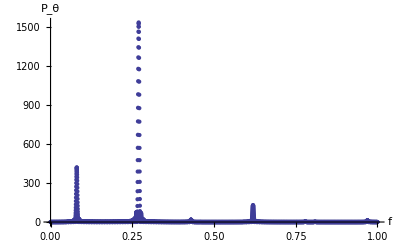

{2012,7,13,1,6,32.1737637}

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=200;xinitial={0,1.3};yinitial={-L0,0};
equs={m x''[t]==-k(1-L0/(√(x[t]^2+y[t]^2)))x[t],m y''[t]==k(-1+L0/(√(x[t]^2+y[t]^2)))y[t]-m g,x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
θ[t_]:=Arg[-y[t]+x[t]*ⅈ];
fs=ps={};const=2.0π;Date[]
Do[real=NIntegrate[θ[t]*Cos[const*f*t],{t,0,tm},MinRecursion->6,MaxRecursion->12,AccuracyGoal->10];imaginary=NIntegrate[θ[t]*Sin[const*f*t],{t,0,tm},MinRecursion->6,MaxRecursion->12,AccuracyGoal->10];AppendTo[fs,{f,real-imaginary ⅈ}];AppendTo[ps,{f,real^2+imaginary^2}],{f,0,1,0.0002}]
ListPlot[ps,PlotRange->All,AxesLabel->{"f","P_θ"}]
Export["e:/thetafs.dat",fs];
Export["e:/thetaps.dat",ps];Date[]
```

```mathematica
Clear[x,y,θ,fs,ps,real,imaginary,average,const,sample]
Clear[g,k,m,L0,tm,equs,s,x,y,η,xinitial,yinitial]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

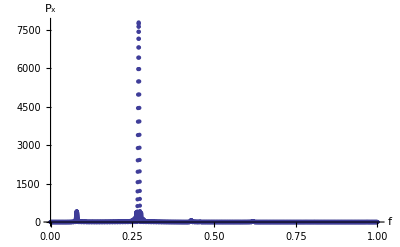

{2012,7,13,1,37,8.408189}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in t near {t} = {73.9914}. NIntegrate obtained 0.000162492 and 2.07854×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in t near {t} = {73.9914}. NIntegrate obtained -0.0000336536 and 1.01681×10^-10 for the integral and error estimates.

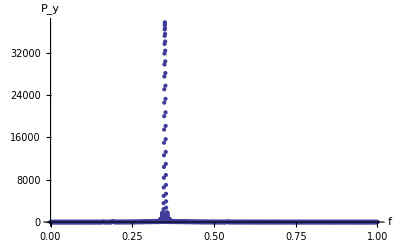

{2012,7,13,2,3,9.9095317}

```mathematica
fs=ps={};
Do[real=NIntegrate[x[t]*Cos[const*f*t],{t,0,tm},MinRecursion->6,MaxRecursion->12,AccuracyGoal->10];imaginary=NIntegrate[x[t]*Sin[const*f*t],{t,0,tm},MinRecursion->6,MaxRecursion->12,AccuracyGoal->10];AppendTo[fs,{f,real-imaginary ⅈ}];AppendTo[ps,{f,real^2+imaginary^2}],{f,0,1,0.0002}]
ListPlot[ps,PlotRange->All,AxesLabel->{"f","P_x"}]
Export["e:/xfs.dat",fs];
Export["e:/xps.dat",ps];Date[]
fs=ps={};sample=2000;
average=NSum[y[t],{t,0,tm,tm/sample}]/sample;
Do[real=NIntegrate[(y[t]-average)*Cos[const*f*t],{t,0,tm},MinRecursion->6,MaxRecursion->12,AccuracyGoal->10];imaginary=NIntegrate[(y[t]-average)*Sin[const*f*t],{t,0,tm},MinRecursion->6,MaxRecursion->12,AccuracyGoal->10];AppendTo[fs,{f,real-imaginary ⅈ}];AppendTo[ps,{f,real^2+imaginary^2}],{f,0,1,0.0002}]
ListPlot[ps,PlotRange->All,AxesLabel->{"f","P_y"}]
Export["e:/yfs.dat",fs];
Export["e:/yps.dat",ps];Date[]
```

```mathematica
(*谱峰的提取与分析*)
```

```mathematica
(*θ的分析*)
```

```mathematica
ps=Import["e:/thetaps.dat"];
len=Length[ps];p=Table[ps[[j,2]],{j,len}];
Emax=Max[p];
unitps=Table[{ps[[j,1]],ps[[j,2]]/Emax},{j,len}];
ListLinePlot[unitps,PlotRange->{{0.2,0.3},{0,0.1}},BaseStyle->{FontSize->13}]
```

```mathematica
Clear[ps,len,p,Emax,unitps]
```

```mathematica
ref=10^-2;
peak={{"Frenquence/Hz","peak"}};
ahead=unitps[[1,2]];middle=unitps[[2,2]];
If[ahead>middle,AppendTo[peak,unitps[[1]]]];
Do[If[(unitps[[j-2,2]]<unitps[[j-1,2]]>unitps[[j,2]])&&(middle>ref),AppendTo[peak,unitps[[j-1]]]];ahead=unitps[[j-1,2]];middle=unitps[[j,2]],{j,3,len}]
peak//TableForm
```

```mathematica
Clear[ref,ahead,middle,peak]
```

```mathematica
(*x的分析*)
```

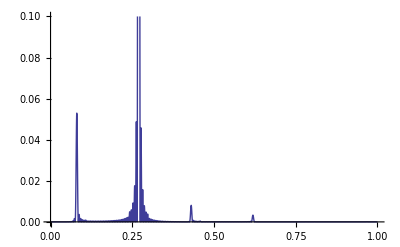

```mathematica
ps=Import["e:/xps.dat"];
len=Length[ps];p=Table[ps[[j,2]],{j,len}];
Emax=Max[p];
unitps=Table[{ps[[j,1]],ps[[j,2]]/Emax},{j,len}];
ListLinePlot[unitps,PlotRange->{{0,1},{0,0.1}},BaseStyle->{FontSize->13}]
```

```mathematica
ref=10^-2;
peak={{"Frenquence/Hz","peak"}};
ahead=unitps[[1,2]];middle=unitps[[2,2]];
If[ahead>middle,AppendTo[peak,unitps[[1]]]];
Do[If[(unitps[[j-2,2]]<unitps[[j-1,2]]>unitps[[j,2]])&&(middle>ref),AppendTo[peak,unitps[[j-1]]]];ahead=unitps[[j-1,2]];middle=unitps[[j,2]],{j,3,len}]
peak//TableForm
```

Frenquence/Hz | peak
0.0804 | 0.0529366
0.2574 | 0.0175611
0.2624 | 0.0487703
0.2696 | 1.
0.2768 | 0.0457574
0.2818 | 0.0156861

```mathematica
(*y的分析*)
```

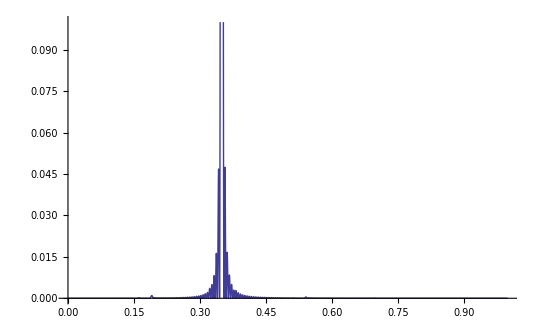

```mathematica
ps=Import["e:/yps.dat"];
len=Length[ps];p=Table[ps[[j,2]],{j,len}];
Emax=Max[p];
unitps=Table[{ps[[j,1]],ps[[j,2]]/Emax},{j,len}];
ListLinePlot[unitps,PlotRange->{{0,1},{0,0.1}},BaseStyle->{FontSize->13}]
```

```mathematica
ref=10^-2;
peak={{"Frenquence/Hz","peak"}};
ahead=unitps[[1,2]];middle=unitps[[2,2]];
If[ahead>middle,AppendTo[peak,unitps[[1]]]];
Do[If[(unitps[[j-2,2]]<unitps[[j-1,2]]>unitps[[j,2]])&&(middle>ref),AppendTo[peak,unitps[[j-1]]]];ahead=unitps[[j-1,2]];middle=unitps[[j,2]],{j,3,len}]
peak//TableForm
```

Frenquence/Hz | peak
0.3374 | 0.0162658
0.3426 | 0.0468135
0.3498 | 1.
0.3568 | 0.0474543
0.362 | 0.0166737